# Pictures for the Geometry Day talk

## Simple examples of totally geodesic submanifolds

### The plane

```mathematica
plane=Graphics3D[Polygon[{{-1,-1,0},{1,-1,0},{1,1,0},{-1,1,0}},VertexColors->{Red,Red,Green,Green}],Boxed->False];
Show[plane,ViewPoint->{1,2,1}]
```

-Graphics3D-

### Great circles

```mathematica
sphere=Graphics3D[{Opacity[0.8],Glow[Blue],Sphere[{0,0,0}]},{Boxed->False}];
vectorPlane=Graphics3D[{Opacity[0.6],Polygon[{{-1.5,-1.5,0},{1.5,-1.5,0},{1.5,1.5,0},{-1.5,1.5,0}},VertexColors->{Orange,Orange,Green,Green}]},{Boxed->False}];
equator=ParametricPlot3D[{Cos[t],Sin[t],0},{t,0,2π},PlotStyle->{Black,Thick}];
greatCircle=Show[sphere,vectorPlane,equator,ViewPoint->{4,1,2}];
greatCircle
```

-Graphics3D-

### Great “hyperbolic planes”

```mathematica
hypSpace=ContourPlot3D[x^2+y^2-z^2==-1,{x,-2,2},{y,-2,2},{z,0,2},Mesh->None,Boxed->False,PlotPoints->140,Axes->False,ContourStyle->Directive[Glow[Blue],Opacity[0.8],Specularity[White,30],ColorFunction->"TemperatureMap"]];
vectorPlane=Graphics3D[{Opacity[0.6],Polygon[{{0,-2,0.5},{0,2,0.5},{0,2,2},{0,-2,2}},VertexColors->{Orange,Orange,Green,Green}]},{Boxed->False}];
hyperbola=ParametricPlot3D[{0,Sinh[t],Cosh[t]},{t,-ArcCosh[2],ArcCosh[2]},PlotStyle->{Black,Thick}];
greatHypPlane=Show[hypSpace,vectorPlane,hyperbola,ViewPoint->{2,3,1}];
greatHypPlane
```

-Graphics3D-

## The lattices Λ and Γ

### The case of Λ

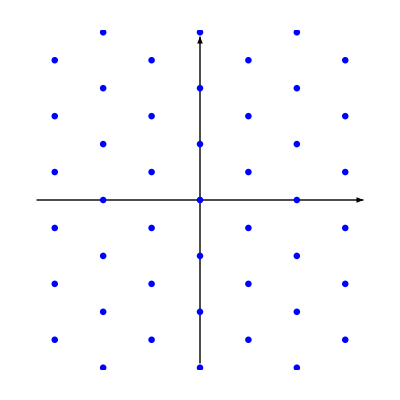

```mathematica
latticeLambda=Graphics[Join[{Thick,Arrow[{{-15,0},{15,0}}],Arrow[{{0,-15},{0,15}}],Blue},Table[Disk[{2 √2 π *n,2 √6 π m/3},0.3],{n,-5,5},{m,-5,5}],Table[Disk[{ √2 π *(2 n + 1),√6 π (2 m + 1)/3},0.3],{n,-5,5},{m,-5,5}]],PlotRange->{{-15,15},{-15,15}}];
Show[latticeLambda]
```

```mathematica
fundamentalDomain=Graphics[{EdgeForm[Thick],LightBlue,Polygon[{{0,0},{√2 π ,√6 π 1/3},{√2 π ,√6 π },{0,2 √6 π/3},{0,0}}],Black,Dashed,Thick,Line[{{√2 π ,√6 π 1/3},{0,2 √6 π/3}}]},PlotRange->{{-15,15},{-15,15}}];
```

```mathematica
{√2 π ,√6 π 1/3}
```

{√2 π,√(2/3) π}

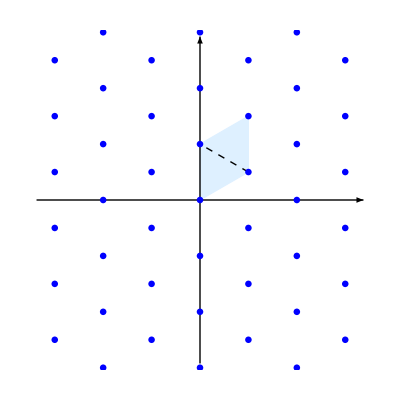

```mathematica
latticeLambdaWithFundamentalDomain=Show[fundamentalDomain,latticeLambda]
```

### The case of Γ

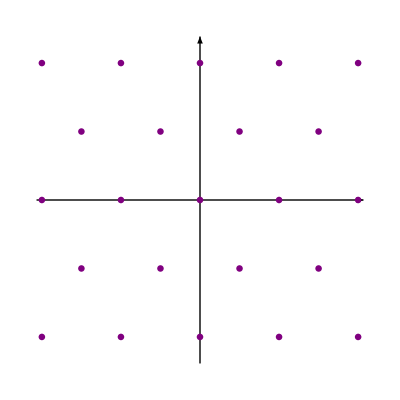

```mathematica
latticeGamma=Graphics[Join[{Thick,Arrow[{{-15,0},{15,0}}],Arrow[{{0,-15},{0,15}}],Purple},Table[Disk[{ 2/(√3)π (n+m),2π (n-m)},0.3],{n,-5,5},{m,-5,5}]],PlotRange->{{-15,15},{-15,15}}]
```

```mathematica
Table[{ 2/(√3)π (n+m),2π (n-m)},{n,-1,2},{m,-1,2}]
```

{{{-(4 π)/(√3),0},{-(2 π)/(√3),-2 π},{0,-4 π},{(2 π)/(√3),-6 π}},{{-(2 π)/(√3),2 π},{0,0},{(2 π)/(√3),-2 π},{(4 π)/(√3),-4 π}},{{0,4 π},{(2 π)/(√3),2 π},{(4 π)/(√3),0},{2 √3 π,-2 π}},{{(2 π)/(√3),6 π},{(4 π)/(√3),4 π},{2 √3 π,2 π},{(8 π)/(√3),0}}}

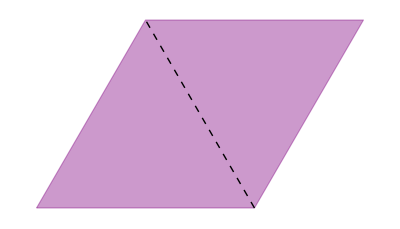

```mathematica
fundamentalDomainGamma=Graphics[{Purple,EdgeForm[Thick],Opacity[0.4],Polygon[{{0,0},{4 π/(√3),0},{2 √3 π,2 π},{(2 π)/(√3),2 π},{0,0}}],Dashed,Black,Opacity[1],Thick,Line[{{4 π/(√3),0},{(2 π)/(√3),2 π}}]}]
```

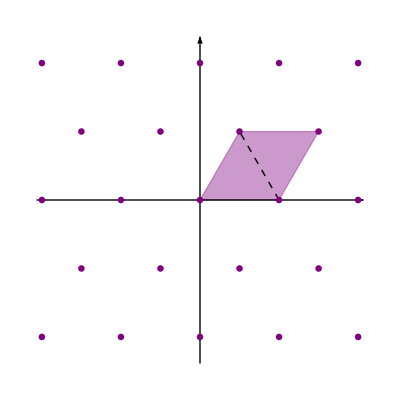

```mathematica
latticeGammaWithFundamentalDomain=Show[fundamentalDomainGamma,latticeGamma,PlotRange->{{-15,15},{-15,15}}];
latticeGammaWithFundamentalDomain
```

## Export images

```mathematica
imageExport[object_,name_]:=Export[StringJoin[NotebookDirectory[],name,".png"],object,ImageResolution->500,Background->None];
```

```mathematica
imageExport[plane,"plane"];
```

```mathematica
imageExport[greatCircle,"greatCircle"];
```

```mathematica
imageExport[greatHypPlane,"greatHypPlane"];
```

```mathematica
imageExport[latticeLambda,"latticeLambda"];
```

```mathematica
imageExport[latticeLambdaWithFundamentalDomain,"latticeLambdaWithFundamentalDomain"];
```

```mathematica
imageExport[latticeGamma,"latticeGamma"];
imageExport[latticeGammaWithFundamentalDomain,"latticeGammaWithFundamentalDomain"];
```